# Učení RBF sítě Demonstrace pokrytí vstupních dat RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, která obsahují dva dobře oddělené shluky dat, každý shluk reprezentuje jednu třídu.
Vygenerujeme tedy tyto dva shluky dat.

```mathematica
values=25;
cluster1 =RandomReal[{1,3},{values,2}];
cluster2=RandomReal[ {5,7},{values,2}];
inData = Join[cluster1,cluster2]
outcluster1=ConstantArray[{1,0},{values}];
outcluster2 = ConstantArray[{0,1},{values}];
outData= Join[outcluster1,outcluster2];
```

{{1.83403,2.64674},{1.7936,2.88009},{2.28776,1.7568},{1.45942,2.07286},{1.45387,2.86388},{2.29352,1.30929},{2.82052,1.98532},{1.17585,1.87471},{1.95457,2.27438},{2.21621,1.02549},{2.25724,2.72045},{2.52092,2.95353},{1.96018,1.54759},{1.0191,1.89338},{1.2354,2.01082},{2.32073,1.98568},{1.10007,2.56423},{1.12144,2.66611},{2.79663,2.03308},{1.05513,1.33495},{2.49819,2.15154},{2.39689,1.41145},{2.74683,1.94101},{1.55,2.15126},{2.6335,2.97842},{6.49716,6.62423},{6.98368,6.16226},{5.34266,6.5317},{5.82196,6.47846},{5.15933,6.07305},{6.38691,6.92657},{5.93413,5.02903},{5.86969,5.84423},{5.79245,6.58803},{6.61546,5.78394},{6.43027,5.62821},{6.61537,6.92549},{5.94197,5.89084},{6.6304,6.59923},{5.48017,5.71863},{6.93795,5.50862},{5.57818,6.03824},{5.34227,6.09518},{6.85977,6.30594},{6.68614,5.61107},{6.19017,5.48119},{6.04303,6.27348},{6.90616,5.58323},{6.44426,5.30769},{6.69252,5.64995}}

Vygenerovaná data si můžeme zobrazit. Každá třída dat má v grafu jinou bavu.

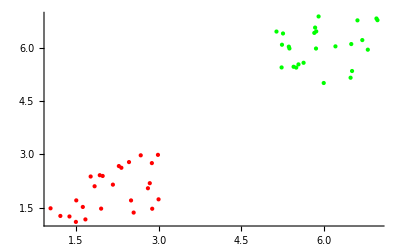

```mathematica
ListPlot[{cluster1,cluster2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě s jedním RBF neuronem, dvěma vstupy a dvěma výstupy.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,1,RandomInitialization->True];
```

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme chtěli.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-15 at 16:27. The network has 2 inputs and 2 outputs.  It consists of 1 basis function of Exp type. The network has a linear submodel.